```mathematica
(*(*Clear all previous definitions to ensure a clean run*)ClearAll["Global`*"];*)

(*************************************************************************)
(*STEP 1:DEFINE THE "GROUND TRUTH" FUNCTION (UNCHANGED)*)
(*************************************************************************)

mfptSingleIntegral[b_?NumericQ]:=Module[{integrand,result},integrand[x_]:=Exp[-x^2/2]*(E^((x/Sqrt[2])^2) Erfc[-x/Sqrt[2]])^2;
result=NIntegrate[integrand[x],{x,-Infinity,b},WorkingPrecision->25];
(Sqrt[Pi]/(2*Sqrt[2]))*result];
mfptAnalytic[b_]:=Module[{integrand,result},integrand[x_]:=Exp[-x^2/2]*(E^((x/Sqrt[2])^2) Erfc[-x/Sqrt[2]])^2;
result=Integrate[integrand[x],{x,-Infinity,b}];
(Sqrt[Pi]/(2*Sqrt[2]))*result];
```

```mathematica
(*************************************************************************)
(*STEP 2:GENERATE OR LOAD PRE-COMPUTED DATA*)
(*************************************************************************)

(*---Parameters to adjust---*)
bMin=-6.0;
bMax=10.0; 
numPoints=4000;
SetDirectory[NotebookDirectory[]]
dataFilename="mfpt_lookup_data.mx";

(*---Check for data file,then load or generate as needed---*)
If[FileExistsQ[dataFilename],(*If file exists,load it instantly*)Print["Loading pre-computed data from \"",dataFilename,"\"..."];
{bValues,tValues}=Import[dataFilename,"MX"];,(*If file doesn't exist,run the one-time generation and save it*)Print["No data file found. Generating new data... (this may take a moment)"];
bValues=Range[bMin,bMax,(bMax-bMin)/(numPoints-1)];
tValues=Monitor[Table[mfptSingleIntegral[b],{b,bValues}],StringForm["Calculating for b = ``",N[b,4]]];
Export[dataFilename,{bValues,tValues},"MX"];
Print["Data generation complete. Saved to \"",dataFilename,"\" for future sessions."];];


(*************************************************************************)
(*STEP 3:CREATE THE FAST HYBRID FUNCTION (UNCHANGED)*)
(*************************************************************************)

splineFunction=Interpolation[Transpose[{bValues,tValues}]];
asymptoticFormula[b_]:=(Sqrt[2*Pi]/b)*Exp[b^2/2];
mfptLowerTail[b_?NumericQ]=Assuming[b<1,(Sqrt[Pi]/(2*Sqrt[2]))*Integrate[Exp[x^2/2](Series[Erfc[-x/Sqrt[2]],{x,-Infinity,5}]//Normal)^2,{x,-Infinity,b}]]//FullSimplify;
fastMFPT[b_?NumericQ]:=Which[b<bMin,mfptLowerTail[b],b>bMax,asymptoticFormula[b],True,splineFunction[b]];
fastMFPT[b_List]:=fastMFPT/@b;


(*************************************************************************)
(*STEP 4:WIDE-RANGE ACCURACY TEST (UNCHANGED)*)
(*************************************************************************)

testPoints=Table[RandomReal[{i,i+1}],{i,-12,12}];
Print[Style["\n--- Wide-Range Accuracy Test (for small b I trust the asymptotics, not the -Exact Value-) ---",Bold,14]];
results=Monitor[Table[Module[{valExact,valApprox,absError,relError},valExact=mfptSingleIntegral[b];
valApprox=fastMFPT[b];
absError=Abs[valExact-valApprox];
relError=If[valExact!=0,absError/valExact,0];
{b,valExact,valApprox,absError,relError}],{b,testPoints}],StringForm["Testing b = ``",N[b,4]]];
tableData=Prepend[results,Item[#,BaseStyle->{"Bold"}]&/@{"b","Exact Value","Approx Value","Abs. Error","Rel. Error"}];
Print[Grid[tableData,Frame->All,Spacings->{2,1},Alignment->{{Left,".",".",".","."}},Background->{None,{Lighter[Gray,.9],{White,Lighter[Blend[{Blue,Green}],.9]}}}]];
```

/Users/btw970/lin_alg/The-Lotka-Volterra-Metacommunity-Model/Infinite_pool_assembly

Loading pre-computed data from "mfpt_lookup_data.mx"...

--- Wide-Range Accuracy Test (for small b I trust the asymptotics, not the -Exact Value-) ---

b | Exact Value | Approx Value | Abs. Error | Rel. Error
-11.4726 | 6.683896264535495506187522×10^-33 | 1.99997×10^-30 | 1.99328×10^-30 | 298.221
-10.0918 | 2.840550016333520449656724×10^-26 | 6.63766×10^-24 | 6.60926×10^-24 | 232.675
-9.28211 | 9.22414241068705585946426×10^-23 | 1.83686×10^-20 | 1.82763×10^-20 | 198.136
-8.01599 | 8.018006864653148711315215×10^-18 | -1.14228×10^-17 | 1.94408×10^-17 | 2.42464
-7.67398 | 1.328546815777999423169408×10^-16 | 1.56141×10^-16 | 2.32863×10^-17 | 0.175276
-6.56057 | 5.719005106624099161538756×10^-13 | 5.7199×10^-13 | 8.99242×10^-17 | 0.000157237
-5.27492 | 2.1035430729498868239224×10^-9 | 2.10354×10^-9 | 8.04407×10^-18 | 3.82406×10^-9
-4.11664 | 9.343241004921500658610185×10^-7 | 9.34324×10^-7 | 1.71746×10^-15 | 1.83818×10^-9
-3.73095 | 5.453502315813710785734265×10^-6 | 5.4535×10^-6 | 3.62955×10^-15 | 6.65545×10^-10
-2.48188 | 0.0006919210609628194116957196 | 0.000691921 | 2.71795×10^-13 | 3.92813×10^-10
-1.78934 | 0.00591770214233653618995581 | 0.0059177 | 1.12926×10^-12 | 1.90827×10^-10
-0.809097 | 0.06918437277748547317566638 | 0.0691844 | 3.79875×10^-12 | 5.49077×10^-11
0.916449 | 1.610589080731050328196075 | 1.61059 | 7.04594×10^-11 | 4.37476×10^-11
1.93203 | 8.572476647890033283057842 | 8.57248 | 1.26549×10^-9 | 1.47623×10^-10
2.71841 | 42.66623729712137360544155 | 42.6662 | 3.36309×10^-9 | 7.88232×10^-11
3.78557 | 934.7879916724069139520516 | 934.788 | 8.43002×10^-7 | 9.01811×10^-10
4.17108 | 3862.738817883516261596975 | 3862.74 | 3.38769×10^-6 | 8.77018×10^-10
5.18276 | 343082.8288136764218503655 | 343083. | 0.0000433387 | 1.26321×10^-10
6.05929 | 3.99937986849391098518915×10^7 | 3.99938×10^7 | 0.0799035 | 1.9979×10^-9
7.60708 | 1.234597185277962274338864×10^12 | 1.2346×10^12 | 6994.47 | 5.66539×10^-9
8.96332 | 7.907467280404472772110567×10^16 | 7.90747×10^16 | 1.09885×10^9 | 1.38963×10^-8
9.00148 | 1.109221052257009261364717×10^17 | 1.10922×10^17 | 4.39589×10^9 | 3.96305×10^-8
10.3647 | 5.190858741212450805795008×10^22 | 5.14159×10^22 | 4.92643×10^20 | 0.00949059
11.1658 | 2.677605417734450372359151×10^26 | 2.65577×10^26 | 2.18358×10^24 | 0.00815497
12.4146 | 5.960225067068490939410998×10^32 | 5.92103×10^32 | 3.9191×10^30 | 0.00657542

```mathematica
(************************************************************************)
```

(I found this rule because Mathematica gave me different formulae when rho -> 1 and for arbitrary rho . The requirement that they are equal for rho == 0 led to this Rule (of which Mathematica seems unaware).
Because this 2F2 converges to zero for negative arguments, It's actually better to use the negative argument form for numerical integration!

```mathematica
Rule2F2=HypergeometricPFQ[{1,1},{3/2,2},s_]:>(π Erf[√s] Erfi[√s])/(2 s)-HypergeometricPFQ[{1,1},{3/2,2},-s]
```

HypergeometricPFQ[{1,1},{3/2,2},s_]:>(π Erf[√s] Erfi[√s])/(2 s)-HypergeometricPFQ[{1,1},{3/2,2},-s]

```mathematica
Series[HypergeometricPFQ[{1,1},{3/2,2},s],{s,0,10}]
Series[HypergeometricPFQ[{1,1},{3/2,2},s]/.Rule2F2,{s,0,10}]
```

1+s/3+(4 s^2)/45+(2 s^3)/105+(16 s^4)/4725+(16 s^5)/31185+(64 s^6)/945945+(16 s^7)/2027025+(256 s^8)/310134825+(256 s^9)/3273645375+(1024 s^10)/151242416325+O[s]^11

1+s/3+(4 s^2)/45+(2 s^3)/105+(16 s^4)/4725+(16 s^5)/31185+(64 s^6)/945945+(16 s^7)/2027025+(256 s^8)/310134825+(256 s^9)/3273645375+(1024 s^10)/151242416325+O[s]^(21/2)

```mathematica
coefficient1=Assuming[n>=-2,SeriesCoefficient[(π Erf[x] Erfi[x])/(2 x^2)-HypergeometricPFQ[{1,1},{3/2,2},-x^2],{x,0,n}]//FullSimplify]
coefficient2=
Assuming[n>=-2,SeriesCoefficient[HypergeometricPFQ[{1,1},{3/2,2},x^2],{x,0,n}]//FullSimplify]

(* Should be possible to proove equality of these by demonstrating that coefficient2 satisfies the recursion equations in coefficient1 *)
```

Piecewise[{{1/2 π [2+n], n<0||Mod[n,2]>0}, {-(ⅈ^n √π)/((2+n) Gamma[(3+n)/2])+1/2 π [2+n], True}}]

Piecewise[{{(√π)/((2+n) Gamma[(3+n)/2]), Mod[n,2]==0&&n≥0}, {0, True}}]

```mathematica
Assuming[Mod[n,2]==0&&n>=0,{coefficient1,coefficient2}//FullSimplify]
%//InputForm
```

{-(ⅈ^n √π)/((2+n) Gamma[(3+n)/2])+1/2 π [2+n],(√π)/((2+n) Gamma[(3+n)/2])}

{-((I^n*Sqrt[Pi])/((2 + n)*Gamma[(3 + n)/2])) + 
  (Pi*DifferenceRoot[Function[{y, n}, 
       {-4*n*y[n] + (1 + n)*(3 + n)*(4 + n)*y[4 + n] == 
         0, y[0] == 0, y[1] == 0, y[2] == 4/Pi, y[3] == 0}]][
     2 + n])/2, Sqrt[Pi]/((2 + n)*Gamma[(3 + n)/2])}

```mathematica
mu[X_]:=rho*(x0-X) (* with rho==1 Mathematica makes simpler results *)
(*mu[X_]:=-X*)a
sigma[X_]:=sig
```

a

```mathematica
V[X_]:=Piecewise[{{0,X>=Xb},{Infinity,X<Xb}}]
fM[X_]:=X
fM2[X_]:=X^2
fM2dt[X_]:=X*(X+mu[X]*dt)
fV[X_]:=1
```

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fM[x]==0&&u[0]==0
uMRule0=DSolve[eqs,u[x],x]//Last//FullSimplify
```

x+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→x/rho+(sig C[1] (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/(√rho)+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
Series[u[x]/.uMRule0/.C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]x0/sig/Sqrt[rho]//FullSimplify,{x,Infinity,1}]//PowerExpand//Simplify
```

1/(2 rho)(-ⅈ ⅈ^(2 Floor[Arg[(2 rho x x0)/sig^2-(rho x0^2)/sig^2]/(2 π)]) π x0+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig x0)/(√rho x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) ((√π sig x0)/(√rho x)+O[1/x]^2)+(2 x+1/sig^2 x0 (ⅈ π sig^2+π sig^2 Erfi[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])-(2 x0^2)/x+O[1/x]^2))

```mathematica
c1RuleM=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]x0/sig/Sqrt[rho]
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π x0)/(√rho sig)

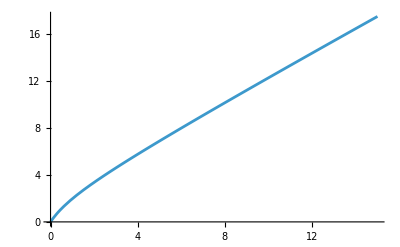

```mathematica
Plot[u[x]/.uMRule0/.c1RuleM/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uMRule=uMRule0/.c1RuleM//Simplify
```

{u[x]→x/rho+(ⅇ^((rho x0^2)/sig^2) √π x0 (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/rho+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fV[x]==0&&u[0]==0
uVRule0=Assuming[rho>0&&sig>0&&x0>0,DSolve[eqs,u[x],x]//Last//FullSimplify]/.Rule2F2//FullSimplify
```

1+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→(sig C[1] (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/(√rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
Series[u[x]/.uVRule0/.C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]/sig/Sqrt[rho]//FullSimplify,{x,Infinity,1}]//PowerExpand//Simplify
```

1/(2 rho)(-ⅈ (-1)^Floor[Arg[(2 rho x x0)/sig^2-(rho x0^2)/sig^2]/(2 π)] π+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig)/(√rho x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) ((√π sig)/(√rho x)+O[1/x]^2)+(1/sig^2(ⅈ π sig^2+π sig^2 Erfi[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])-(2 x0)/x+O[1/x]^2))

```mathematica
c1RuleV=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]/sig/Sqrt[rho]
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π)/(√rho sig)

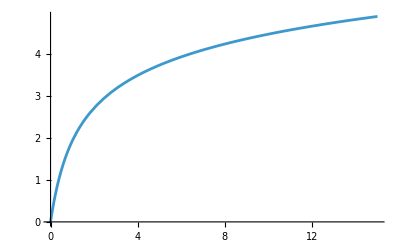

```mathematica
Plot[u[x]/.uVRule0/.c1RuleV/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uVRule=uVRule0/.c1RuleV//FullSimplify
```

{u[x]→(π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
(* Compare this to mean first passage time function: *)

u[x]/.uVRule/.x0->0
Sqrt[Pi]*Integrate[Exp[x^2](1+Erf[x]),{x,0,b},GenerateConditions->False]//FunctionExpand//Expand
```

(π Erfi[(√rho x)/sig])/(2 rho)-(x^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x^2)/sig^2])/sig^2

1/2 π Erfi[b]+b^2 HypergeometricPFQ[{1,1},{3/2,2},b^2]

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fM2[x]==0&&u[0]==0
uM2Rule0=Assuming[rho>0&&sig>0&&x0>0,DSolve[eqs,u[x],x]//Last//FullSimplify]/.Rule2F2//FullSimplify
```

x^2+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→1/(2 rho)(x (x+2 x0)+2 ⅇ^((rho x (x-2 x0))/sig^2) √rho sig C[1] DawsonF[(√rho (x-x0))/sig]+2 √rho sig C[1] DawsonF[(√rho x0)/sig]+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))}

```mathematica
Series[u[x]/.uM2Rule0/.C[1]->a*Sqrt[Pi]*Exp[rho x0^2/sig^2](sig^2+2 rho x0^2)/sig/Sqrt[rho]/(2rho),{x,Infinity,1}]//PowerExpand
```

ⅈ^(2 Floor[Arg[(2 rho x x0)/sig^2-(rho x0^2)/sig^2]/(2 π)]) (-(ⅈ a π sig^2)/(4 rho^2)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^2) ((a √π sig^3)/(4 rho^(5/2) x)+O[1/x]^2)+ⅈ^(2 Floor[Arg[(2 rho x x0)/sig^2-(rho x0^2)/sig^2]/(2 π)]) (-(ⅈ a π x0^2)/(2 rho)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^2) ((a √π sig x0^2)/(2 rho^(3/2) x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig (sig^2+2 rho x0^2))/(4 rho^(5/2) x)+O[1/x]^2)+(x^2/(2 rho)+(x0 x)/rho+1/(4 rho^2 sig^2)(sig^2+2 rho x0^2) (ⅈ π sig^2+2 a ⅇ^((rho x0^2)/sig^2) √π sig^2 DawsonF[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])+(-sig^2 x0-2 rho x0^3)/(2 rho^2 x)+O[1/x]^2)

```mathematica
c1RuleM2=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2](sig^2+2 rho x0^2)/sig/Sqrt[rho]/(2rho)
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π (sig^2+2 rho x0^2))/(2 rho^(3/2) sig)

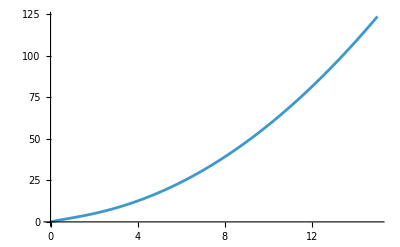

```mathematica
Plot[u[x]/.uM2Rule0/.c1RuleM2/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uM2Rule=uM2Rule0/.c1RuleM2//FullSimplify
```

{u[x]→1/(2 rho)(x (x+2 x0)+(π (sig^2+2 rho x0^2) (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))}

```mathematica
intV=integrate[(u[x]/.uVRule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
intM=integrate[(u[x]/.uMRule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
intM2=integrate[(u[x]/.uM2Rule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
```

integrate[1/(√π sig)ⅇ^(-(rho (x-x0)^2)/sig^2) √rho ((π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

integrate[1/(√π sig)ⅇ^(-(rho (x-x0)^2)/sig^2) √rho (x/rho+(ⅇ^((rho x0^2)/sig^2) √π x0 (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/rho+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

integrate[1/(2 √π √rho sig)ⅇ^(-(rho (x-x0)^2)/sig^2) (x (x+2 x0)+(π (sig^2+2 rho x0^2) (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

```mathematica
simpleInt=PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x]*((π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))/.rho->1/.sig->1//FullSimplify
```

1/(√π)ⅇ^(-(x-x0)^2) (1/2 π (Erfi[x-x0]+Erfi[x0])-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(x-x0)^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},x0^2])

```mathematica
simpleIntegral[x0_]:=
fastMFPT[Sqrt[2]*x0]
```

```mathematica
simpleIntegral[0.0]-(Log[2]/2)
simpleIntegral[0]=Log[2]/2
(*WolframAlpha[ToString[%],IncludePods->"PossibleClosedForm"]*)
```

-1.11753×10^-11

Log[2]/2

```mathematica
simpleIntegral[c]//Timing
fastMFPT[Sqrt[2]*3]//Timing
mfptSingleIntegral[Sqrt[2]*3]//Timing
```

{0.000014,fastMFPT[√2 c]}

{0.000019,5117.26}

{0.018769,5117.259942826081699642779}

```mathematica
restoreRule={x0->x0*Sqrt[rho]/sig,x->x Sqrt[rho]/sig}
integrandRule=Solve[integrand==simpleInt/.HypergeometricPFQ[{1,1},{3/2,2},x0^2]->hyper/.restoreRule//Simplify,hyper]/.hyper->(HypergeometricPFQ[{1,1},{3/2,2},x0^2]/.restoreRule)//Last//FullSimplify
```

{x0→(√rho x0)/sig,x→(√rho x)/sig}

{HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]→1/(2 rho x0^2)(2 ⅇ^((rho (x-x0)^2)/sig^2) integrand √π sig^2-π sig^2 (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig])+2 rho (x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2])}

```mathematica
intVS=intV/.integrandRule//FullSimplify
intMS=intM/.integrandRule//FullSimplify
intM2S=intM2/.integrandRule//FullSimplify
```

integrate[integrand/(√rho sig),{x,0,∞}]

integrate[((ⅇ^(-(rho (x-x0)^2)/sig^2) x)/(√π)+integrand x0)/(√rho sig),{x,0,∞}]

integrate[((ⅇ^(-(rho (x-x0)^2)/sig^2) rho x (x+2 x0))/(√π)+integrand (sig^2+2 rho x0^2))/(2 rho^(3/2) sig),{x,0,∞}]

```mathematica
{intVS1,intMS1,intM2S1}=Assuming[rho>0&&sig>9,{intVS,intMS,intM2S}/.integrand->0/.integrate->Integrate]//FullSimplify
```

{0,((ⅇ^(-(rho x0^2)/sig^2) sig)/(√π)+√rho x0 (1+Erf[(√rho x0)/sig]))/(2 rho^(3/2)),((6 ⅇ^(-(rho x0^2)/sig^2) √rho sig x0)/(√π)+(sig^2+6 rho x0^2) (1+Erf[(√rho x0)/sig]))/(8 rho^2)}

```mathematica
intVS2=D[intVS[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
intMS2=D[intMS[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
intM2S2=D[intM2S[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
```

fastMFPT[(√2 √rho x0)/sig]/rho

(x0 fastMFPT[(√2 √rho x0)/sig])/rho

((sig^2+2 rho x0^2) fastMFPT[(√2 √rho x0)/sig])/(2 rho^2)

```mathematica
$Assumptions=SD>0 && rho>0
RuleSD=Solve[SD==sig/Sqrt[2*rho],sig]//Last
```

SD>0&&rho>0

{sig→√2 √rho SD}

```mathematica
intVSFull=intVS1+intVS2/.RuleSD//FullSimplify
intMSFull=intMS1+intMS2/.RuleSD//FullSimplify
intM2SFull=intM2S1+intM2S2/.RuleSD//FullSimplify
```

fastMFPT[x0/SD]/rho

(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD+x0+x0 Erf[x0/(√2 SD)]+2 x0 fastMFPT[x0/SD])/(2 rho)

(3 ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD x0+(SD^2+3 x0^2) (1+Erf[x0/(√2 SD)])+4 (SD^2+x0^2) fastMFPT[x0/SD])/(4 rho)

```mathematica
meanXstart=Assuming[rho>0&&sig>0,Integrate[x*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]/Integrate[PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]//FullSimplify//PowerExpand//FullSimplify]/.RuleSD//FullSimplify
```

x0+(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD)/(1+Erf[x0/(√2 SD)])

```mathematica
meanRichness=arrivalRate*intVSFull
meanX=Apart[arrivalRate*intMSFull/meanRichness,fastMFPT[x0/SD]]
meanX2=Apart[arrivalRate*intM2SFull/meanRichness,fastMFPT[x0/SD]]
meanXstart
(*(X*(X+mu[X]*dt)//Expand)/.X^2->meanX2/.X->meanX//FullSimplify*)
```

(arrivalRate fastMFPT[x0/SD])/rho

x0+(ⅇ^(-x0^2/(2 SD^2)) (√(2/π) SD+ⅇ^(x0^2/(2 SD^2)) x0+ⅇ^(x0^2/(2 SD^2)) x0 Erf[x0/(√2 SD)]))/(2 fastMFPT[x0/SD])

SD^2+x0^2+1/(4 fastMFPT[x0/SD])ⅇ^(-x0^2/(2 SD^2)) (ⅇ^(x0^2/(2 SD^2)) SD^2+3 √(2/π) SD x0+3 ⅇ^(x0^2/(2 SD^2)) x0^2+ⅇ^(x0^2/(2 SD^2)) SD^2 Erf[x0/(√2 SD)]+3 ⅇ^(x0^2/(2 SD^2)) x0^2 Erf[x0/(√2 SD)])

x0+(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD)/(1+Erf[x0/(√2 SD)])

```mathematica
meanFieldEquation=s-x-competition
meanEquation=s-x0-competitionMean
```

-competition+s-x

-competitionMean+s-x0

```mathematica
Solve[meanFieldEquation==0,x]//Last
x0Rule=Solve[meanEquation==0,x0]//Last
```

{x→-competition+s}

{x0→-competitionMean+s}

... now compute mean and variance of competition term following our previous work, taking into account that x0 (“y-bar”) is not a constant but correlated with mean x in the computation of the correlation of the lagged second uncentred moment. In the double sum over independent abundances and in the computation of the first moment of the competition term, x0 (“y-bar”) must be substituted by the mean of x0 over extant species (x0 * intVSFull averaged over the distribution of s); but this might cancel out and so not be needed. 

[[Also take into account that meanX2Sum might already includes the effect of a Poisson-distributed variation in species richness. But I’m not sure: its computation does not make use of the fact that species arrival and colonisation are  Poisson processes, it would go the same if arrivals were clocked. That’s still something to think about. Then again, dividing meanX2Sum by meanRichness also feels wrong. Perhaps rather make sure that meanX2Sum takes the Poisson arrival process into account, which might be different from simply multiplying with arrivalRate? One way to find this out would be to compute the corresponding quantity for fixed s and compare with out original work.]] The issue with the Poisson distributed species richness arises only for the double sum over first moments. In this case, looking at means per species and multiplying with Poisson distributed richness squared is correct. In other case, the summation over richness simply removes the division by richness from the averaging, so it is harmless.

```mathematica
normaliser=1
highProportion = .;
lowProportion = 1- highProportion
highS = 1;
lowS = 8/10;
sAveraged[expression_/;!FreeQ[expression,x0]]:=sAveraged[expression/.x0Rule]
sAveraged[expression_/;FreeQ[expression,rho|competitionMean|SD]]:=
highProportion*(expression/.s->highS)+lowProportion*(expression/.s->lowS)
sAveraged2[expression_/;Not[FreeQ[expression,s]]]:=
highProportion*(expression/.s->highS)+lowProportion*(expression/.s->lowS)
```

1

1-highProportion

```mathematica
?sAveraged
```

```mathematica
selfConsist1=-competitionMean+II*CC*sAveraged[arrivalRate*intMSFull]/.rho->rho*arrivalRate//FullSimplify
```

-competitionMean+CC II sAveraged[(ⅇ^(-(competitionMean-s)^2/(2 SD^2)) SD)/(√(2 π) rho)-1/(2 rho)(competitionMean-s) (1+Erf[(-competitionMean+s)/(√2 SD)]+2 fastMFPT[(-competitionMean+s)/SD])]

```mathematica
selfConsist2=-SD^2+II^2*CC*sAveraged[intM2SFull]/.arrivalRate->1//FullSimplify
```

-SD^2+CC II^2 sAveraged[1/(4 rho)(3 ⅇ^(-(competitionMean-s)^2/(2 SD^2)) √(2/π) (-competitionMean+s) SD+(3 (competitionMean-s)^2+SD^2) (1+Erf[(-competitionMean+s)/(√2 SD)])+4 ((competitionMean-s)^2+SD^2) fastMFPT[(-competitionMean+s)/SD])]

```mathematica
selfConsist3=Assuming[rho>0,sAveraged[x0*intMSFull]/.rho->1//FullSimplify]
```

sAveraged[(ⅇ^(-(competitionMean-s)^2/(2 SD^2)) (-competitionMean+s) SD)/(√(2 π))+1/2 (competitionMean-s)^2 (1+Erf[(-competitionMean+s)/(√2 SD)]+2 fastMFPT[(-competitionMean+s)/SD])]

```mathematica
Block[{II=4/10,CC=4/10,SESI=(1-II*CC)^2/(II^2*CC*(1-CC)),Ey=Sqrt[2/Pi]/Log[2],Ey2=(1+1/Log[4]),SPRED=SESI/Ey2,SDPRED=(Ey2/Ey)II^2*CC*(1-CC)/(II*CC*(1-II*CC))},
SPRED]//N
```

10.6748

```mathematica
table=Table[Block[{II=4/10,CC=4/10,SESI=(1-II*CC)^2/(II^2*CC*(1-CC)),Ey=Sqrt[2/Pi]/Log[2],Ey2=(1+1/Log[4]),SPRED=SESI/Ey2,SDPRED=(Ey2/Ey)II^2*CC*(1-CC)/(II*CC*(1-II*CC)),competitionMeanPRED=sAveraged[s],rhoPRED=Log[2]/SPRED},
(*Print[{rhoPRED,competitionMeanPRED,SDPRED,SPRED}//N];*)
targetFunction[a_?NumericQ,b_?NumericQ,c_?NumericQ]:={selfConsist1,selfConsist2,selfConsist3}/.{rho->a,competitionMean->b,SD->c};
fr=FindRoot[targetFunction[rho1,competitionMean1,SD1],{{rho1,rhoPRED},{competitionMean1,competitionMeanPRED},{SD1,SDPRED}},MaxIterations->1000];
(*Print[{targetFunction[rho1,competitionMean1,SD1]}/.fr];*)
fr=fr/.{rho1->rho,competitionMean1->competitionMean,SD1->SD};
fr=Prepend[fr,highProp->highProportion];
(*Print[fr];*)
fr
],{highProportion,0,1,1/100}]/.highProp->highProportion;
```

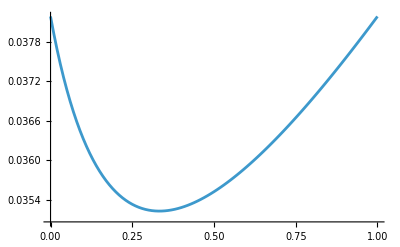

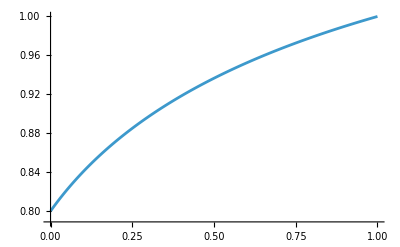

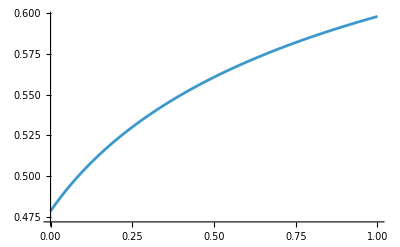

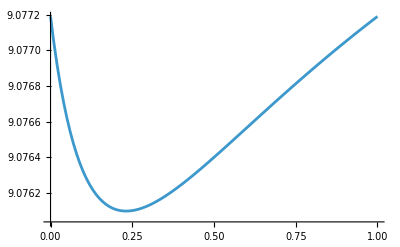

```mathematica
ListPlot[{highProportion,rho}/.table,Joined->True]
ListPlot[{highProportion,competitionMean}/.table,Joined->True]
ListPlot[{highProportion,SD}/.table,Joined->True]
ListPlot[{highProportion,sAveraged2[meanRichness/.x0Rule/.arrivalRate->1]}/.table,Joined->True]
```

```mathematica
pInv[s_]=1-CDF[NormalDistribution[x0,SD]][0]/.x0Rule
```

1-1/2 Erfc[(-competitionMean+s)/(√2 SD)]

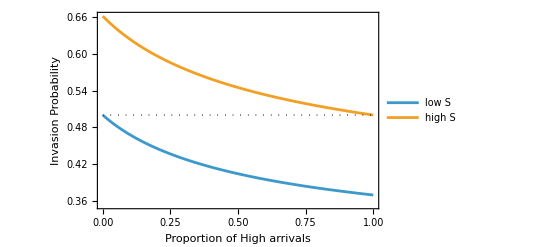

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
ListPlot[{{highProportion,pInv[lowS]}/.table,{highProportion,pInv[highS]}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low S","high S"},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Invasion Probability"}]
pInvLow=Interpolation[{highProportion,pInv[lowS]}/.table]
pInvHigh=Interpolation[{highProportion,pInv[highS]}/.table]
```

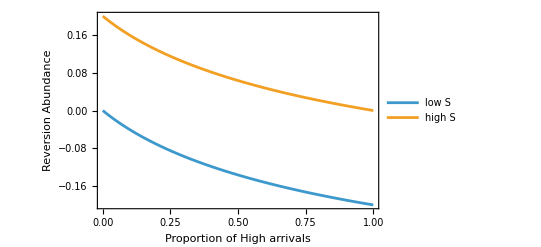

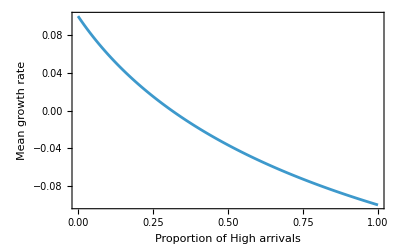

```mathematica
ListPlot[{{highProportion,s-competitionMean/.x0Rule/.s->lowS}/.table,{highProportion,s-competitionMean/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Reversion Abundance"}]
ListPlot[{highProportion,((s-competitionMean/.x0Rule/.s->lowS)+(s-competitionMean/.x0Rule/.s->highS))/2}/.table,Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean growth rate"}]
```

x0+(ⅇ^(-x0^2/(2 SD^2)) (√(2/π) SD+ⅇ^(x0^2/(2 SD^2)) x0+ⅇ^(x0^2/(2 SD^2)) x0 Erf[x0/(√2 SD)]))/(2 fastMFPT[x0/SD])

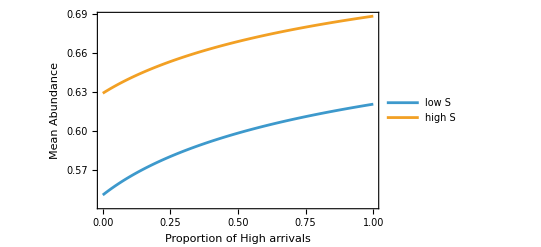

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
meanX
ListPlot[{{highProportion,meanX/.x0Rule/.s->lowS}/.table,{highProportion,meanX/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Abundance"}]
abundanceLow=Interpolation[{highProportion,meanX/.x0Rule/.s->lowS}/.table]
abundanceHigh=Interpolation[{highProportion,meanX/.x0Rule/.s->highS}/.table]
```

9.07719

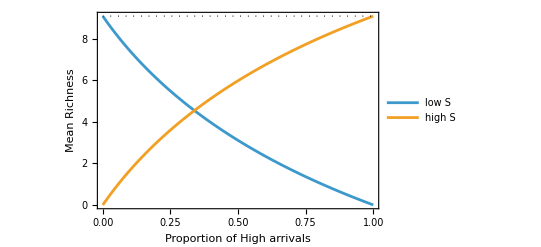

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
pureS = intVSFull/.x0Rule/.s->lowS/.table[[1]]
ListPlot[{{highProportion,(1-highProportion)*intVSFull/.x0Rule/.s->lowS}/.table,{highProportion,highProportion*intVSFull/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,pureS},{1,pureS}}]},PlotLegends->{"low S","high S"},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Richness"}]
durationLow=Interpolation[{highProportion,(1-highProportion)*intVSFull/.x0Rule/.s->lowS}/.table]
durationHigh=Interpolation[{highProportion,highProportion*intVSFull/.x0Rule/.s->highS}/.table]
```

(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD+x0+x0 Erf[x0/(√2 SD)]+2 x0 fastMFPT[x0/SD])/(2 rho)

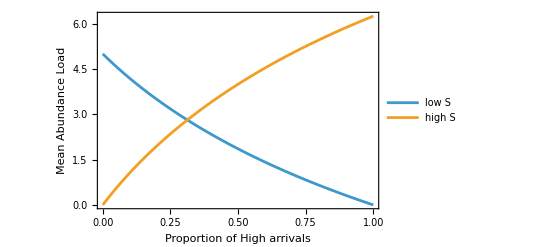

InterpolatingFunction[…]

InterpolatingFunction[…]

1/(2 π (1+r^2)^(3/2))

```mathematica
intMSFull
ListPlot[{{highProportion,(1-highProportion)*intMSFull/.x0Rule/.s->lowS}/.table,{highProportion,highProportion*intMSFull/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,pureS},{1,pureS}}]},PlotLegends->{"low S","high S"},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Abundance Load"}]
loadLow=Interpolation[{highProportion,(1-highProportion)*intMSFull/.x0Rule/.s->lowS}/.table]
loadHigh=Interpolation[{highProportion,highProportion*intMSFull/.x0Rule/.s->highS}/.table]
```

```mathematica
bExp=6/4
rRange=1
dDensity[r_]=(bExp-1)/(Pi*rRange^2)(1+(r/rRange)^2)^(-bExp)
Integrate[(bExp-1)/(Pi*rRange^2)(1+(r/rRange)^2)^(-bExp)*r*2*Pi,{r,0,Infinity}]
```

3/2

1

1/(2 π (1+r^2)^(3/2))

1

```mathematica
NX = NY =20
environment[{x_,y_}]:=HeavisideTheta[y-(NY/2)-1/2]+1
env=Table[environment[{1,y}],{y,1,NY}]
```

20

{1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2}

11

11

{0.212801,0.207827,0.0818411,0.0399757,0.0227984,0.014363,0.00967845,0.00684424,0.00501958,0.00378847,0.00292679,0.00378847,0.00501958,0.00684424,0.00967845,0.014363,0.0227984,0.0399757,0.0818411,0.207827}

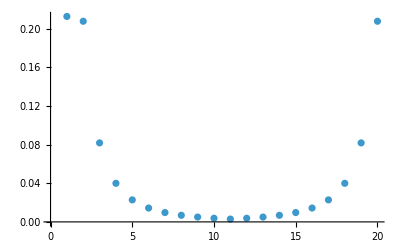

```mathematica
dKernelRaw=Table[dDensity[Sqrt[dx^2+dy^2]],{dy,-NY/2,NY/2-1},{dx,-NX/2,NX/2-1}]//N;
kernelCentreX=NX/2+1
kernelCentreY=NY/2+1
dKernelRaw[[kernelCentreX,kernelCentreY]]=0;
dKernelRaw=dKernelRaw/Total[dKernelRaw,2];
yKernel=RotateRight[Total[dKernelRaw,{2}],NY/2]
ListPlot[yKernel]
```

```mathematica
abundance1=loadHigh[1](2-env)
alpha2=loadHigh[1](env-1)
highProp=Table[1/2,NY]
oneProp=(2-env)
```

{6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25}

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
For[ii=1,ii<1000,ii++,incoming1=InverseFourier[Fourier[abundance1]*Fourier[yKernel]]//Chop;
incoming2=InverseFourier[Fourier[abundance2]*Fourier[yKernel]]//Chop;
incoming=incoming1+incoming2;
oneProp=incoming1/incoming;
abundance1=MapThread[#1[[#2]]&,{{loadHigh[oneProp],loadLow[1-oneProp]}//Transpose,env}];
abundance2=MapThread[#1[[#2]]&,{{loadLow[oneProp],loadHigh[1-oneProp]}//Transpose,env}];
]
```

```mathematica
theoryBiomass=ListPlot[{abundance1,abundance2},PlotRange->{0,Automatic},PlotLegends->{"Biomass 1 (theory)", "Biomass 2 (theory)"},PlotMarkers->"□"]
```

-Graphics-

```mathematica
biomassSim=Import["biomass_by_type.csv", HeaderLines->{1,1}]//Transpose
```

{{6.0342,6.3643,6.2802,6.4879,6.4386,6.3775,6.3664,6.4719,6.1744,5.9398,1.2443,0.9591,0.7301,0.7457,0.4607,0.7157,0.7566,0.9573,0.9869,1.2603},{0.8227,0.504,0.5816,0.4388,0.5082,0.5958,0.5686,0.4674,0.7552,0.7676,5.5021,5.9275,6.2095,6.3085,6.6763,6.7298,6.224,6.1733,6.1525,5.5189}}

```mathematica
simlationBiomass=ListPlot[{biomassSim[[1]],biomassSim[[2]]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Biomass 1 (sim)", "Biomass 2 (sim)"},
PlotMarkers->"●"]
```

-Graphics-

```mathematica
Show[simlationBiomass,theoryBiomass]
```

-Graphics-

```mathematica
(* Unsing this solution, now compute species-level dispersal parameter: *)
```

```mathematica
pInv1=MapThread[#1[[#2]]&,{{pInvHigh[oneProp],pInvLow[1-oneProp]}//Transpose,env}]
pInv2=MapThread[#1[[#2]]&,{{pInvLow[oneProp],pInvHigh[1-oneProp]}//Transpose,env}]
alpha1=MapThread[#1[[#2]]&,{{durationHigh[oneProp],durationLow[1-oneProp]}//Transpose,env}]
alpha2=MapThread[#1[[#2]]&,{{durationLow[oneProp],durationHigh[1-oneProp]}//Transpose,env}]
meanAbundance1=abundance1/alpha1
meanAbundance2=abundance2/alpha2
meanLifetime1=alpha1/pInv1 (* in units of propagule attivals *)
meanLifetime2=alpha2/pInv2 (* in units of propagule attivals *)
```

{0.535843,0.521442,0.514755,0.511462,0.510069,0.510069,0.511462,0.514755,0.521442,0.535843,0.396635,0.385476,0.38033,0.377804,0.376738,0.376738,0.377804,0.38033,0.385476,0.396635}

{0.396635,0.385476,0.38033,0.377804,0.376738,0.376738,0.377804,0.38033,0.385476,0.396635,0.535843,0.521442,0.514755,0.511462,0.510069,0.510069,0.511462,0.514755,0.521442,0.535843}

{6.56231,7.52871,7.99697,8.23233,8.33284,8.33284,8.23233,7.99697,7.52871,6.56231,2.51422,1.54805,1.07992,0.844617,0.744142,0.744142,0.844617,1.07992,1.54805,2.51422}

{2.51422,1.54805,1.07992,0.844617,0.744142,0.744142,0.844617,1.07992,1.54805,2.51422,6.56231,7.52871,7.99697,8.23233,8.33284,8.33284,8.23233,7.99697,7.52871,6.56231}

{0.672767,0.678878,0.681816,0.683288,0.683915,0.683915,0.683288,0.681816,0.678878,0.672767,0.602827,0.609822,0.613167,0.614837,0.615549,0.615549,0.614837,0.613167,0.609822,0.602827}

{0.602827,0.609822,0.613167,0.614837,0.615549,0.615549,0.614837,0.613167,0.609822,0.602827,0.672767,0.678878,0.681816,0.683288,0.683915,0.683915,0.683288,0.681816,0.678878,0.672767}

{12.2467,14.4383,15.5355,16.0957,16.3367,16.3367,16.0957,15.5355,14.4383,12.2467,6.33886,4.01595,2.83942,2.23559,1.97522,1.97522,2.23559,2.83942,4.01595,6.33886}

{6.33886,4.01595,2.83942,2.23559,1.97522,1.97522,2.23559,2.83942,4.01595,6.33886,12.2467,14.4383,15.5355,16.0957,16.3367,16.3367,16.0957,15.5355,14.4383,12.2467}

```mathematica
Export["metacommunity_fields.csv",Join[{{"pColonisation1","pColonisation2","meanAbundance1","meanAbundance2","extirpationRate1","extirpationRate2"}},Transpose[{pInv1,pInv2,meanAbundance1,meanAbundance2,incoming/meanLifetime1,incoming/meanLifetime2}]]]
```

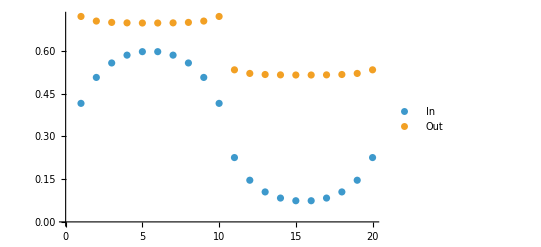

```mathematica
ListPlot[{incoming1*pInv1,incoming*alpha1/meanLifetime1},PlotLegends->{"In","Out"}]
```

```mathematica
(* OLD CODE COMPUTING FIRST ALPHA AND THEN ABUNDANCE: *)
```

```mathematica
alpha1=10*(2-env)
alpha2=10*(env-1)
highProp=Table[1/2,NY]
oneProp=(2-env)
```

{10,10,10,10,10,10,10,10,10,10,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,10,10,10,10,10,10,10,10,10,10}

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
For[ii=1,ii<1000,ii++,abundance1=alpha1*MapThread[#1[[#2]]&,{{abundanceHigh[oneProp],abundanceLow[1-oneProp]}//Transpose,env}];
abundance2=alpha2*MapThread[#1[[#2]]&,{{abundanceLow[oneProp],abundanceHigh[1-oneProp]}//Transpose,env}];
incoming1=InverseFourier[Fourier[abundance1]*Fourier[yKernel]]//Chop;
incoming2=InverseFourier[Fourier[abundance2]*Fourier[yKernel]]//Chop;
oneProp=incoming1/(incoming1+incoming2);
alpha1=MapThread[#1[[#2]]&,{{durationHigh[oneProp],durationLow[1-oneProp]}//Transpose,env}];
alpha2=MapThread[#1[[#2]]&,{{durationLow[oneProp],durationHigh[1-oneProp]}//Transpose,env}]
]
```

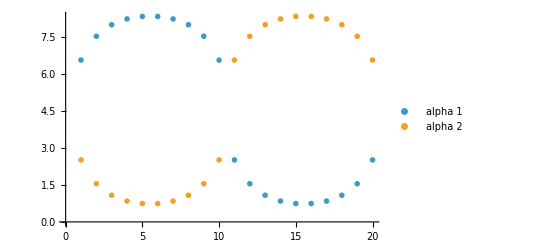

```mathematica
theoryAlpha=ListPlot[{alpha1,alpha2},PlotRange->{0,Automatic},PlotLegends->{"alpha 1", "alpha 2"},PlotMarkers->"OpenMarkers"]
```

```mathematica
alphaSim=Drop[Import["alpha_by_type.csv"],1]//Transpose
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{15.5,16.45,17.1,16.7,17.2,17.85,16.75,17.1,16.55,15.2,15.65,16.6,17.1,17.,17.6,16.7,16.65,16.55,16.05,14.75},{3.4,2.2,2.1,1.15,1.25,2.1,1.85,2.1,2.65,4.1,4.35,2.05,2.,1.9,1.35,2.3,2.55,2.55,3.45,4.}}

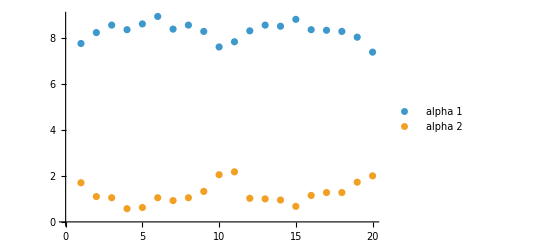

```mathematica
simlationAlpha=ListPlot[{alphaSim[[2]],alphaSim[[3]]}/2//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"alpha 1", "alpha 2"}]
```

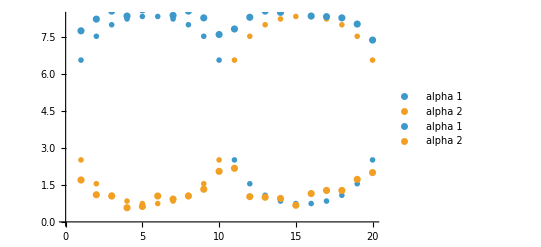

```mathematica
Show[theoryAlpha,simlationAlpha]
```